```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<< package.wl;
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
InputField[Dynamic[string],String,FieldHint->"Inserisci una funzione discontinua"]
```

Plotta la funzione:

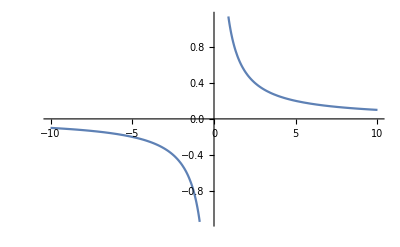

```mathematica
Button["Plotta la funzione: ",Print[Plot[Evaluate[ToExpression[string,TraditionalForm]],{x,-10,10}]]]
```

```mathematica
(* Calcoliamo il limite della funzione scritta dall'utente *)
```

```mathematica
LimitCalculator[f_,x_]:= Block[{data,list},Grid[{
pdisc = Solve[FunctionSingularities[f,x],Reals];
	list = Table[Last[Last[pdisc[[i]]]],{i,Length[pdisc]}];
Table[
With[{data00=data},
Button[StringJoin["Calcola il Limite nel punto:  " ,ToString[data00]],Print[StringJoin["Il valore del limite nel punto ",ToString[data00]," è: ", ToString[Limit[f,x-> data00,Direction->1]]]]]],{data,list}]}]
]
```

```mathematica
Button["Calcola il limite",LimitCalculator[string,x]]
```

Calcola il limite